```mathematica
ρ=dw/(π((w-w0)^2+dw^2));
Integrate[ρ Sin[w t]/w,{w,-∞,∞}]
```

ConditionalExpression[-1/(2 π (dw^2+w0^2) Abs[t])t (-2 dw π+dw π Cosh[(dw-ⅈ w0) Abs[t]]+ⅈ π w0 Cosh[(dw-ⅈ w0) Abs[t]]+dw π Cosh[(dw+ⅈ w0) Abs[t]]-ⅈ π w0 Cosh[(dw+ⅈ w0) Abs[t]]+(-ⅈ dw+w0) CosIntegral[(-ⅈ dw-w0) Abs[t]] Sinh[(dw-ⅈ w0) Abs[t]]+ⅈ (dw+ⅈ w0) CosIntegral[(ⅈ dw+w0) Abs[t]] Sinh[(dw-ⅈ w0) Abs[t]]+ⅈ dw CosIntegral[ⅈ (dw+ⅈ w0) Abs[t]] Sinh[(dw+ⅈ w0) Abs[t]]+w0 CosIntegral[ⅈ (dw+ⅈ w0) Abs[t]] Sinh[(dw+ⅈ w0) Abs[t]]-ⅈ dw CosIntegral[(-ⅈ dw+w0) Abs[t]] Sinh[(dw+ⅈ w0) Abs[t]]-w0 CosIntegral[(-ⅈ dw+w0) Abs[t]] Sinh[(dw+ⅈ w0) Abs[t]]-ⅈ dw Cosh[(dw-ⅈ w0) Abs[t]] SinhIntegral[(dw-ⅈ w0) Abs[t]]+w0 Cosh[(dw-ⅈ w0) Abs[t]] SinhIntegral[(dw-ⅈ w0) Abs[t]]+dw Cosh[(dw-ⅈ w0) Abs[t]] SinIntegral[(ⅈ dw+w0) Abs[t]]+ⅈ w0 Cosh[(dw-ⅈ w0) Abs[t]] SinIntegral[(ⅈ dw+w0) Abs[t]]),t∈ℝ&&Im[w0]≠Re[dw]&&Im[w0]+Re[dw]≠0]

```mathematica
Simplify[%,Assumptions->{dw>0,w0>0,t>0}]
```

-1/(2 π (dw^2+w0^2))(-2 dw π+dw π Cosh[t (dw-ⅈ w0)]+ⅈ π w0 Cosh[t (dw-ⅈ w0)]+dw π Cosh[t (dw+ⅈ w0)]-ⅈ π w0 Cosh[t (dw+ⅈ w0)]+ⅈ (dw+ⅈ w0) CosIntegral[t (ⅈ dw+w0)] Sinh[t (dw-ⅈ w0)]+(-ⅈ dw+w0) CosIntegral[-ⅈ dw t-t w0] Sinh[t (dw-ⅈ w0)]-ⅈ dw CosIntegral[t (-ⅈ dw+w0)] Sinh[t (dw+ⅈ w0)]-w0 CosIntegral[t (-ⅈ dw+w0)] Sinh[t (dw+ⅈ w0)]+ⅈ dw CosIntegral[ⅈ dw t-t w0] Sinh[t (dw+ⅈ w0)]+w0 CosIntegral[ⅈ dw t-t w0] Sinh[t (dw+ⅈ w0)]-ⅈ dw Cosh[t (dw-ⅈ w0)] SinhIntegral[t (dw-ⅈ w0)]+w0 Cosh[t (dw-ⅈ w0)] SinhIntegral[t (dw-ⅈ w0)]+dw Cosh[t (dw-ⅈ w0)] SinIntegral[t (ⅈ dw+w0)]+ⅈ w0 Cosh[t (dw-ⅈ w0)] SinIntegral[t (ⅈ dw+w0)])

```mathematica
Gt=-1/(2 π (dw^2+w0^2))(-2 dw π+dw π Cosh[t (dw-ⅈ w0)]+ⅈ π w0 Cosh[t (dw-ⅈ w0)]+dw π Cosh[t (dw+ⅈ w0)]-ⅈ π w0 Cosh[t (dw+ⅈ w0)]+ⅈ (dw+ⅈ w0) CosIntegral[t (ⅈ dw+w0)] Sinh[t (dw-ⅈ w0)]+(-ⅈ dw+w0) CosIntegral[-ⅈ dw t-t w0] Sinh[t (dw-ⅈ w0)]-ⅈ dw CosIntegral[t (-ⅈ dw+w0)] Sinh[t (dw+ⅈ w0)]-w0 CosIntegral[t (-ⅈ dw+w0)] Sinh[t (dw+ⅈ w0)]+ⅈ dw CosIntegral[ⅈ dw t-t w0] Sinh[t (dw+ⅈ w0)]+w0 CosIntegral[ⅈ dw t-t w0] Sinh[t (dw+ⅈ w0)]-ⅈ dw Cosh[t (dw-ⅈ w0)] SinhIntegral[t (dw-ⅈ w0)]+w0 Cosh[t (dw-ⅈ w0)] SinhIntegral[t (dw-ⅈ w0)]+dw Cosh[t (dw-ⅈ w0)] SinIntegral[t (ⅈ dw+w0)]+ⅈ w0 Cosh[t (dw-ⅈ w0)] SinIntegral[t (ⅈ dw+w0)]);
```

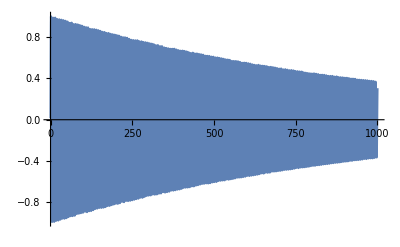

```mathematica
Plot[Gt/.{dw->.001,w0->1},{t,0,1000},PlotRange->All]
```

```mathematica
f=(u^2-1)/(u^2+1)^2/.{u->(w0-w)/dw};
g=2u/(u^2+1)^2/.{u->(w0-w)/dw};
Gt=Simplify[-I/(2π) Integrate[(f+I g)Exp[-I w t]/dw,{w,-∞,∞}],Assumptions->{dw>0,w0>0,t>0}]
```

(dw t (ⅈ π-CosIntegral[t (-ⅈ dw+w0)]+CosIntegral[ⅈ dw t-t w0]) (Cosh[t (dw+ⅈ w0)]-Sinh[t (dw+ⅈ w0)]))/(2 π)

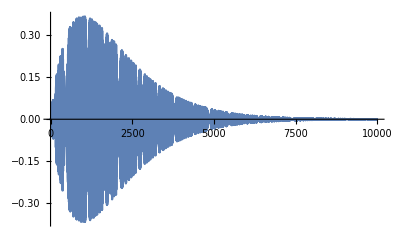

```mathematica
Plot[Re[Gt/.{dw->.001,w0->1}],{t,0,10000},PlotRange->All]
```

```mathematica
Gw=Integrate[Gt Exp[I w t],{t,0,∞}]
```

ConditionalExpression[-1/(4 π (dw^2+w0^2))(-(4 ⅈ dw π)/w+(2 ⅈ dw π w)/(w^2+(dw-ⅈ w0)^2)-(2 π w w0)/(w^2+(dw-ⅈ w0)^2)+(2 ⅈ dw π w)/(dw^2+w^2+2 ⅈ dw w0-w0^2)+(2 π w w0)/(dw^2+w^2+2 ⅈ dw w0-w0^2)+(dw ArcTan[(√(-(dw-ⅈ w0)^2))/(dw+ⅈ (w-w0))])/(dw+ⅈ (w-w0))+(w0 ArcTan[(√(-(dw-ⅈ w0)^2))/(dw+ⅈ (w-w0))])/(-ⅈ dw+w-w0)-(w0 ArcTan[(√(-(dw-ⅈ w0)^2))/(dw-ⅈ (w+w0))])/(ⅈ dw+w+w0)+(dw ArcTan[(√(-(dw-ⅈ w0)^2))/(dw-ⅈ (w+w0))])/(dw-ⅈ (w+w0))+(√((dw-ⅈ w0)^2) (dw+ⅈ w0) ArcTanh[(dw-ⅈ w0)/(dw+ⅈ (w-w0))])/((dw-ⅈ w0) (ⅈ dw-w+w0))+(√((dw-ⅈ w0)^2) (-ⅈ dw+w0) ArcTanh[(ⅈ dw+w0)/(ⅈ dw+w+w0)])/((dw-ⅈ w0) (dw-ⅈ (w+w0)))),Abs[Im[w0]-Re[dw]]<Im[w]&&Abs[Im[w0]+Re[dw]]<Im[w]&&Im[w]>0]

```mathematica
Simplify[-1/(4 π (dw^2+w0^2))(-(4 ⅈ dw π)/w+(2 ⅈ dw π w)/(w^2+(dw-ⅈ w0)^2)-(2 π w w0)/(w^2+(dw-ⅈ w0)^2)+(2 ⅈ dw π w)/(dw^2+w^2+2 ⅈ dw w0-w0^2)+(2 π w w0)/(dw^2+w^2+2 ⅈ dw w0-w0^2)+(dw ArcTan[(√(-(dw-ⅈ w0)^2))/(dw+ⅈ (w-w0))])/(dw+ⅈ (w-w0))+(w0 ArcTan[(√(-(dw-ⅈ w0)^2))/(dw+ⅈ (w-w0))])/(-ⅈ dw+w-w0)-(w0 ArcTan[(√(-(dw-ⅈ w0)^2))/(dw-ⅈ (w+w0))])/(ⅈ dw+w+w0)+(dw ArcTan[(√(-(dw-ⅈ w0)^2))/(dw-ⅈ (w+w0))])/(dw-ⅈ (w+w0))+(√((dw-ⅈ w0)^2) (dw+ⅈ w0) ArcTanh[(dw-ⅈ w0)/(dw+ⅈ (w-w0))])/((dw-ⅈ w0) (ⅈ dw-w+w0))+(√((dw-ⅈ w0)^2) (-ⅈ dw+w0) ArcTanh[(ⅈ dw+w0)/(ⅈ dw+w+w0)])/((dw-ⅈ w0) (dw-ⅈ (w+w0)))),Assumptions->{dw>0,w0>0,w>0}]
```

(ⅈ dw (dw^2+w^2+w0^2))/(w (dw^4+(w^2-w0^2)^2+2 dw^2 (w^2+w0^2)))